```mathematica
CalcGoodForTuple[{3,5,7,11},10]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

Aborted at value : 3

$Aborted

```mathematica
CloseStreams[]
```

```mathematica
RatioSubGood[tuple_, subTuple_, range_] := Module[
{vote, count, countGood, distances, div, result},
count=0;
vote = 0;
div=1;
countGood=0;
result={};
Monitor[
While[count ≤ range,
distances = ParallelTable[Distance[vote,p],{p,tuple}];
If[Min[distances]==0, count++];
If[Max[Table[distances[[p]],{p, subTuple}]] ==0,
countGood = countGood+1;
];
If[Mod[count,div]==0,
result =Append[result,{div,countGood/(count)}];
PrintTemporary[{div,countGood/(count)}];
div=div*Product[tuple[[p]],{p,subTuple}];
];
If [Max[distances] == 0,
vote+=1,
vote += Max[distances]
];
],
{count, range,div}
];
Print[result];
Return[result];
]
```

```mathematica
RatioSubGood[{3,5},{1},3^8]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{1,1}

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

{3,2/3}

{9,2/3}

{27,19/27}

{81,53/81}

{243,157/243}

{729,472/729}

{2187,1418/2187}

{6561,1421/2187}

{{1,1},{3,2/3},{9,2/3},{27,19/27},{81,53/81},{243,157/243},{729,472/729},{2187,1418/2187},{6561,1421/2187}}

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

{{1,1},{5,4/5},{25,18/25},{125,92/125},{625,446/625},{3125,2199/3125},{15625,11071/15625},{78125,11051/15625},{390625,55283/78125},{1953125,1381869/1953125}}

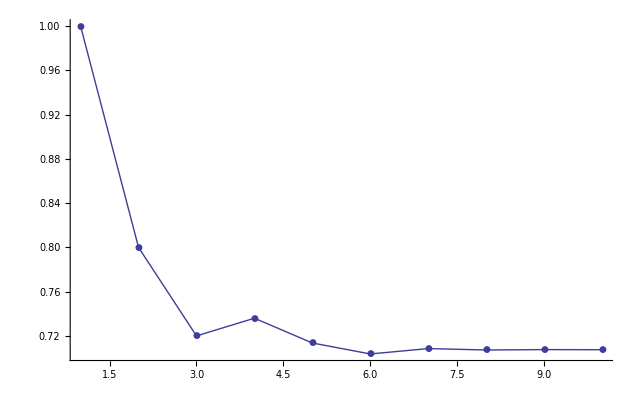

```mathematica
ListPlot[Map[#[[2]]&,RatioSubGood[{3,5},{2},3^14]], Joined->True,PlotMarkers->Automatic, PlotRange->All]
```

```mathematica
v=Map[#[[1]]*#[[2]]&,{{1,1},{5,4/5},{25,18/25},{125,92/125},{625,446/625},{3125,2199/3125},{15625,11071/15625},{78125,11051/15625},{390625,55283/78125},{1953125,1381869/1953125}}]
```

{1,4,18,92,446,2199,11071,55255,276415,1381869}

```mathematica
v={1,4,18,92,446,2199,11071,55255,276415,4259/6561*19683}
```

{1,4,18,92,446,2199,11071,55255,276415,12777}

```mathematica
w=Map[#[[1]]*#[[2]]&,v]
```

{1,2,6,19,53,157,472,1418,4263,12777,38266,114838,344579,1033322,3099499}

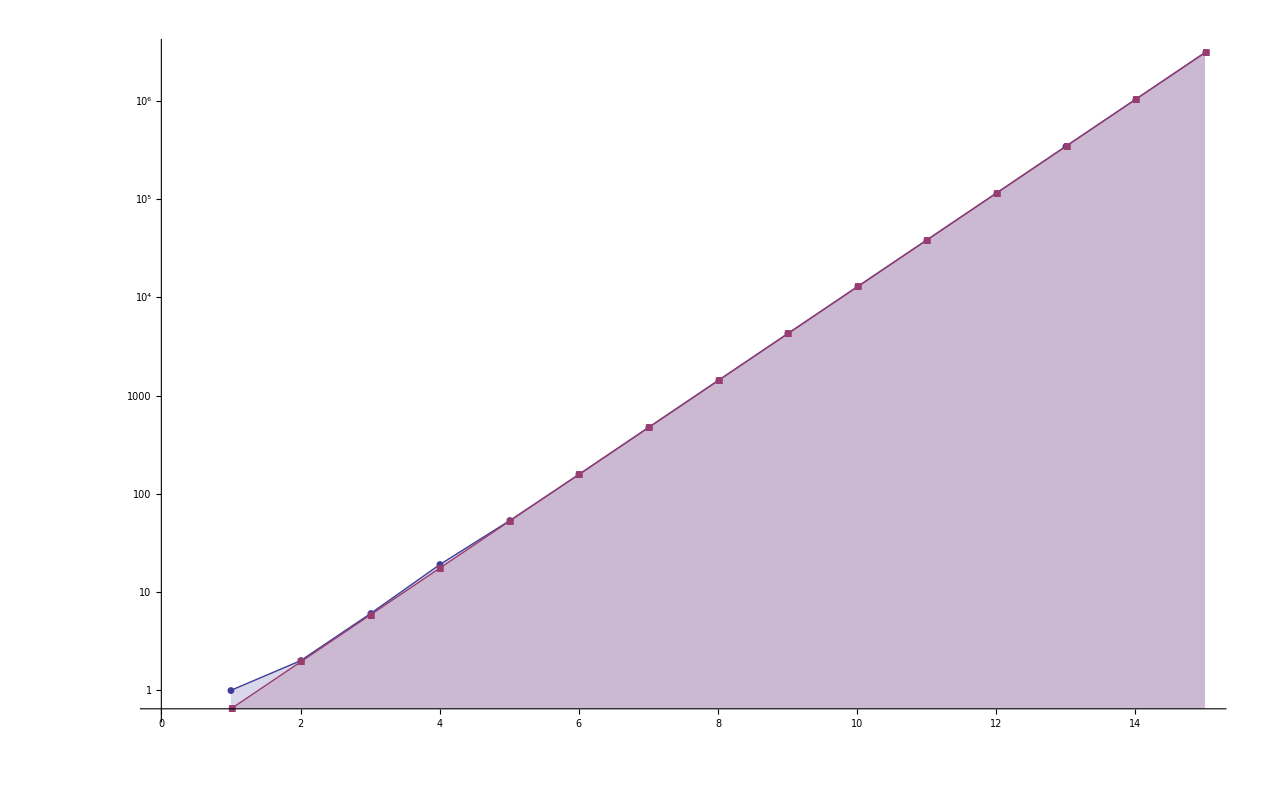

```mathematica
ListLogPlot[{w, With[{a=0.21601404102481395},Table[a  3^x,{x,1,15}]]},Joined->True,Filling->Axis, PlotMarkers->Automatic]
```

```mathematica
FindFit[v, (Pi-a)  5^x,{a,b},x]
```

{a→3.00009,b→0.}

```mathematica
N[1/3*(10+3*3^(1/6))^(1/2)*3^(1/2)]
```

2.12938

```mathematica
N[Sqrt[2]]
```

1.41421

```mathematica
ListPlot[Map[#[[2]]&,RatioSubGood[{3,5},{2},3^16]], Joined->True,PlotMarkers->Automatic, PlotRange->All]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

$Aborted

```mathematica
ListPlot[Map[#[[2]]&,RatioSubGood[{3,5},{1},3^14+1]], Joined->True,PlotMarkers->Automatic, PlotRange->All]
```

$Aborted

```mathematica
ListPlot[Map[#[[2]]&,RatioSubGood[{3,5},{2},5^14+1]], Joined->True,PlotMarkers->Automatic, PlotRange->All]
```